```mathematica
v[x_]:=1/(√(1+Exp[2 x])){1,Exp[x]}
```

```mathematica
Simplify[Norm[v[x]],Assumptions->Element[x,Reals]]
```

1

```mathematica
Nv[x_]:=D[v[x],x]/Norm[D[v[x],x]]
```

```mathematica
Nv[x]
```

{-ⅇ^(2 x)/((1+ⅇ^(2 x))^(3/2) √(ⅇ^(4 Re[x])/(Abs[1+ⅇ^(2 x)]^3)+Abs[-ⅇ^(3 x)/((1+ⅇ^(2 x))^(3/2))+ⅇ^x/(√(1+ⅇ^(2 x)))]^2)),(-ⅇ^(3 x)/((1+ⅇ^(2 x))^(3/2))+ⅇ^x/(√(1+ⅇ^(2 x))))/(√(ⅇ^(4 Re[x])/(Abs[1+ⅇ^(2 x)]^3)+Abs[-ⅇ^(3 x)/((1+ⅇ^(2 x))^(3/2))+ⅇ^x/(√(1+ⅇ^(2 x)))]^2))}

```mathematica
FullSimplify[%,Element[x,Reals]]
```

{-ⅇ^x/(√(1+ⅇ^(2 x))),1/(√(1+ⅇ^(2 x)))}

```mathematica
Simplify[Norm[Nv[x]],Element[x,Reals]]
```

1

```mathematica
k[x_]:=Exp[x]*(1+Exp[2 x])^(-3/2)
```

```mathematica
k[x]
```

ⅇ^x/((1+ⅇ^(2 x))^(3/2))

```mathematica
rh[x_]:=1/k[x]
```

```mathematica
rh[x]
```

ⅇ^-x (1+ⅇ^(2 x))^(3/2)

```mathematica
p[x]
```

{-ⅇ^x (1+ⅇ^(2 x))+x,1+ⅇ^x+ⅇ^(2 x)}

```mathematica
p[x_]:=FullSimplify[{x,Exp[x]}+Nv[x]*rh[x],Assumptions->Element[x,Reals]]
```

```mathematica
p[x]
```

{-1-ⅇ^(2 x)+x,3 Cosh[x]+Sinh[x]}

```mathematica
p1:=Plot[Exp[x],{x,-2,1.5},AspectRatio -> 1,PlotRange->{{-2,1.5},{0,4}}]
```

```mathematica
p[b]
```

{-3/2-Log[2]/2,3 Cosh[Log[2]/2]-Sinh[Log[2]/2]}

```mathematica
p[x_]:={-1-Exp[2 x]+x,3 Cosh[x]+Sinh[x]}
```

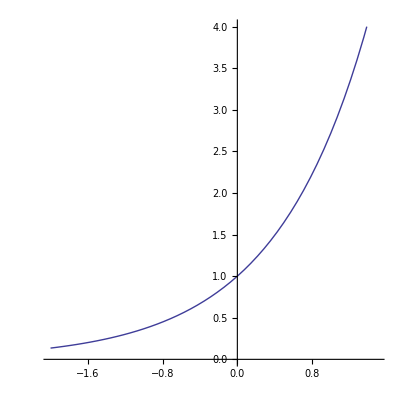

```mathematica
Show[p1]
```

```mathematica
p[a_]:={a,Exp[a]}+(1+Exp[2 a]) {-Exp[a],1}
```

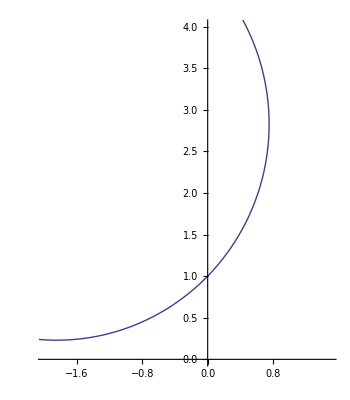

```mathematica
ParametricPlot[p[b]+(1+Exp[2 b])^(3/2)/Exp[b]{Cos[t],Sin[t]},{t,0,2 Pi},PlotRange->{{-2,1.5},{0,4}}]
```

```mathematica
p2:=ParametricPlot[p[b]+((1+Exp[2 b])^(3/2) {Cos[t],Sin[t]})/Exp[b],{t,0,2 π},PlotRange->{{-2,1.5},{0,4}},AspectRatio->1]
```

```mathematica
Show[p1,p2]
```

-Graphics-

```mathematica
b:=Log[Sqrt[1/2]]
```

```mathematica
Clear[b]
```

```mathematica
Manipulate[Show[Plot[Exp[x],{x,-60,1.5},PlotRange->{{-6,1.5},{0,6}},AspectRatio->Automatic,Epilog->{PointSize[0.02],Point[{b,Exp[b]}]}],ParametricPlot[p[b]+((1+Exp[2 b])^(3/2) {Cos[t],Sin[t]})/Exp[b],{t,0,2 π},PlotRange->{{-6,1.5},{0,6}},AspectRatio->Automatic]],{{b,Log[Sqrt[1/2]]},-6,1.5,0.001}]
```

```mathematica
N[Log[Sqrt[1/2]]]
```

-0.346574

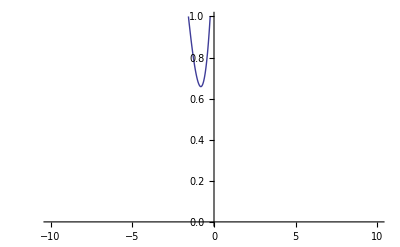

```mathematica
Plot[-Log[Exp[x]/((1+Exp[2x])^3/2)],{x,-10,10},PlotRange->{0,1}]
```